# Mathematica Basics

## Computer Graphics, Wolfram Mathematica

```mathematica
SetOptions[{Plot,Plot3D,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,Graphics,Graphics3D,SphericalPlot3D,DensityPlot,DensityPlot3D,ContourPlot,SliceContourPlot3D,SliceDensityPlot3D,RegionPlot,RegionPlot3D,Graphics3D,RevolutionPlot3D},ImageSize->Small];
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->True,LineSpacing->{1.5,0}];
```

```mathematica
(* === Chapter 1 === *)
```

```mathematica
{15./40,15/40,Cos[Pi/6.],Cos[Pi/6]}
```

{0.375,3/8,0.866025,(√3)/2}

```mathematica
f11[x_]:=Sin[x^2]+Cos[x]
```

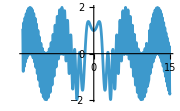

```mathematica
Plot[f11[x],{x,-14,15}]
```

```mathematica
f12[x_]:=Sin[x]+6/(1+x^2)-2
```

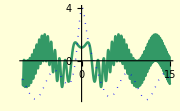

```mathematica
Plot[{f11[x],f12[x]},{x,-10,15},PlotStyle->{{RGBColor[0.2,0.6,0.4],Thickness[0.01]},{Blue,Thick,Dotted}},Background->LightYellow]
```

```mathematica
M1={{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

```mathematica
{MatrixForm[M1],M1[[2]],M1[[2]][[1]]}
```

{(1 | 2 | 3
4 | 5 | 6),{4,5,6},4}

```mathematica
f13[x_,y_]:=x^2+y^2
```

```mathematica
Plot3D[f13[x,y],{x,-1,1},{y,-2,2}]
```

-Graphics3D-

```mathematica
{f13[1+a,Sqrt[1+a+a^2]],Simplify[f13[1+a,Sqrt[1+a+a^2]]]}
```

{1+a+a^2+(1+a)^2,2+3 a+2 a^2}

```mathematica
fx11[t_]:=t+3
fy11[t_]:=2t+3
ft11[t_]:={fx11[t],fy11[t]}
```

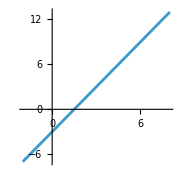

```mathematica
ParametricPlot[ft11[t],{t,-5,5},AspectRatio->1]
```